```mathematica
ClearAll["Global`*"]
```

```mathematica
eval=({{kx^2+ky^2,v},{v,(kx-1)^2+ky^2}}//Eigenvalues) /.{v->-0.04,ky->0}(*analytic eigenvalue for the 2 lower branches*);
```

```mathematica
eig=({{kx^2+ky^2,v},{v,(kx-1)^2+ky^2}}//Eigenvectors)/.{v->-0.04,ky->0};
```

```mathematica
eig1=eig[[1]]/Sqrt[(eig[[1,1]]^2+eig[[1,2]]^2)];
```

```mathematica
eig2=eig[[2]]/Sqrt[(eig[[2,1]]^2+eig[[2,2]]^2)];
V={{0,-0.04,-0.04,-0.04,-0.04,-0.02,-0.02,-0.02,-0.02},{-0.04,0,0,-0.02,-0.02,-0.04,0,-0.04,0},{-0.04,0,0,-0.02,-0.02,0.,-0.04,0,-0.04},{-0.04,-0.02,-0.02,0,0,-0.04,0,0,-0.04},{-0.04,-0.02,-0.02,0,0,0,-0.04,-0.04,0},{-0.02,-0.04,0,-0.04,0,0,0,0,0},{-0.02,0,-0.04,0,-0.04,0,0,0,0},{-0.02,-0.04,0,0,-0.04,0,0,0,0},{-0.02,0,-0.04,-0.04,0,0,0,0,0}};
H0={kx^2+ky^2,(kx+1)^2+ky^2,(kx-1)^2+ky^2,kx^2+(ky+1)^2,kx^2+(ky-1)^2,(kx+1)^2+(ky-1)^2,(kx-1)^2+(ky-1)^2,(kx+1)^2+(ky-1)^2,(kx-1)^2+(ky+1)^2}(*Used by En1 and En2*);
H0ofdiag=DiagonalMatrix[{kx^2+ky^2,(kx+1)^2+ky^2,(kx-1)^2+ky^2,kx^2+(ky+1)^2,kx^2+(ky-1)^2,(kx+1)^2+(ky-1)^2,(kx-1)^2+(ky-1)^2,(kx+1)^2+(ky-1)^2,(kx-1)^2+(ky+1)^2}](*Used by evalOfNineByNine*);
```

```mathematica
evalOfNineByNine=(Eigenvalues[(H0ofdiag+V)/.{ky->0}])[[1;;2]];
```

```mathematica
En1=eval[[1]]+Conjugate[eig1[[1]]*V[[2,1]]+eig1[[2]]*V[[2,3]]]*(eig1[[1]]*V[[2,1]]+eig1[[2]]*V[[2,3]])/(eval[[1]]-H0[[2]])+Sum[(eig1[[1]]*V[[j,1]]+eig1[[2]]*V[[j,3]])^2/(eval[[1]]-H0[[j]]),{j,4,9}]/.ky->0(*After add second order energy correction*);
En2=eval[[2]]+Conjugate[eig2[[1]]*V[[2,1]]+eig2[[2]]*V[[2,3]]]*(eig2[[1]]*V[[2,1]]+eig2[[2]]*V[[2,3]])/(eval[[2]]-H0ofdiag[[2,2]])+Sum[(eig2[[1]]*V[[j,1]]+eig2[[2]]*V[[j,3]])^2/(eval[[2]]-H0ofdiag[[j,j]]),{j,4,9}]/.ky->0(*After add second order energy correction*);
```

```mathematica
freeBranch={kx^2,(kx-1)^2};
```

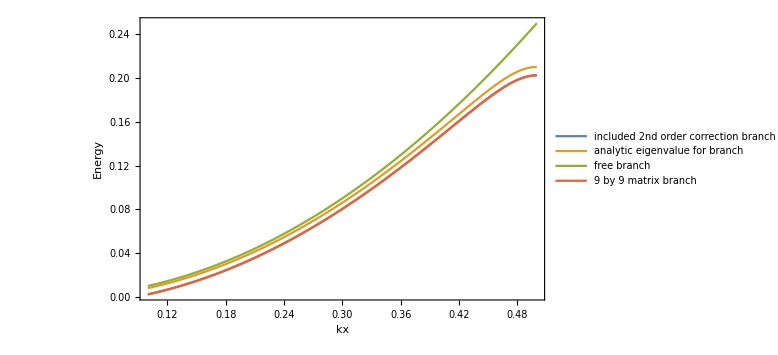

```mathematica
Plot[{En1,eval[[1]],freeBranch[[1]],evalOfNineByNine[[1]]},{kx,0.1,1/2},PlotRange->Full,ImageSize->Large,Frame->True,FrameLabel->{{Energy,None},{kx,None}},PlotLegends->{"included 2nd order correction branch","analytic eigenvalue for branch","free branch","9 by 9 matrix branch"},PlotPoints->2000]
```